# Smale Horse Shoe Map

The plan is to make a simple map with complicated dynamics.   That leaves the pill shaped region S unchanged

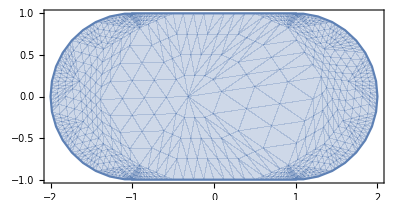

```mathematica
S=RegionUnion[ Rectangle[{-1,-1},{1,1}],Disk[{-1,0},1],Disk[{1,0},1]];
RegionPlot[S,AspectRatio->Automatic]
```

## Squish

```mathematica
s1[a_][{x_,y_}]:={x,a*y}
a=0.4;
ParametricPlot[{{x,y},s1[a][{x,y}]},
{x,y}∈S]
```

-Graphics-

## Stretch

```mathematica
s2[a_][{x_,y_}]:={x/a,y}
ParametricPlot[{{x,y},s2[a][s1[a][{x,y}]]},
{x,y}∈S]
```

-Graphics-

## Fold

```mathematica
fold[b_][{x_,y_}]:=Module[{r, θ},
r=Sqrt[x^2+y^2];
θ=
```

# Finding Periodic Sequences in 2D

For a function f:ℝ^2→ℝ^2  consider the sequence defined recursively by 
	p_(n+1)=f(p_n)
and an initial value p_0∈ℝ^2. We will make smoothness assumptions about f as we need them.  We learned that we will never see an unstable periodic orbit by iterating. We learned that a stable periodic orbit with a tiny stability region was also very hard to find!

Some pictures would probably help.

## Ex 1

The first thing we did in ℝ^1 was plot our function of interest with the “do-nothing” identity function.  This only worked because we had one spare dimension in which to plot.  We do not have two spare dimensions when we are in ℝ^2!

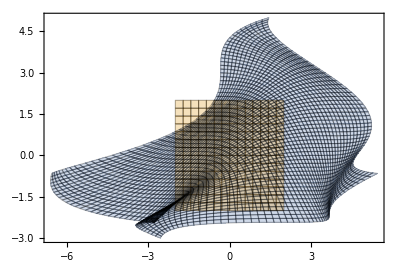

```mathematica
f[{x_,y_}]:= {0.1+x +2y+ Cos[x *y], y-x + Cos[x+y]}
ParametricPlot[{ f[{x,y}],{x,y}},{x,-2,2},{y,-2,2},
Mesh->All]
```

Then we decided we could plot get rid of the spare dimension by subtracting our function from the identity function.  We can now see that there is one fixed point:  The bad news is we have no idea which value of {x,y} it comes from!

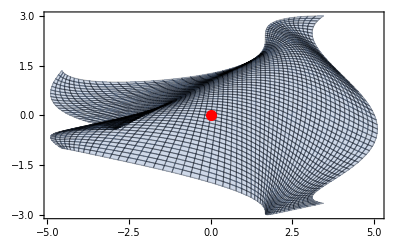

```mathematica
ParametricPlot[f[{x,y}]-{x,y},{x,-2,2},{y,-2,2},
Mesh->All,
Epilog->{Red, PointSize[0.02], Point[{0,0}]}]
```

what we need to do is plot both coordinate bits that make the picture above together in a way that ties them back to the where they came from.  Not too bad!

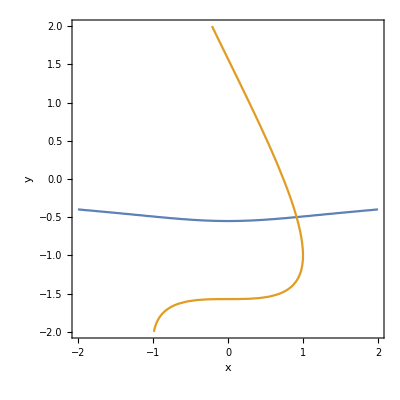

```mathematica
ContourPlot[{f[{x,y}]⟦1⟧==x,f[{x,y}]⟦2⟧==y},{x,-2,2},{y,-2,2},
Mesh->All,
FrameLabel->{"x","y"}]
```

Once we have a decent initial guess we can compute the fixed point!

```mathematica
FPSub=FindRoot[f[{x,y}]=={x,y},{x,1},{y,-0.1}]
```

{x→0.91475,y→-0.498841}

The bad news is we do not know if there are other solutions further out in x and/or y!   We would like to know if this is stable.  First a picture.

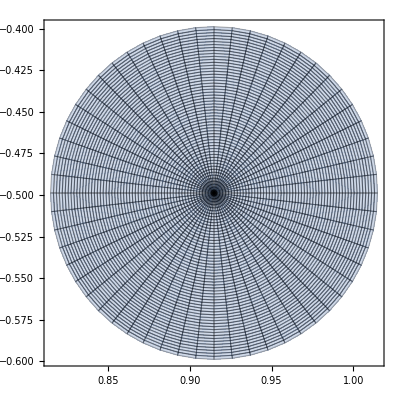

```mathematica
FP={x,y}/.FPSub;
ParametricPlot[ FP+r {Cos[θ],Sin[θ]},
{θ,0, 2π},{r, 0, 0.1},
Mesh->All]
```

### Break

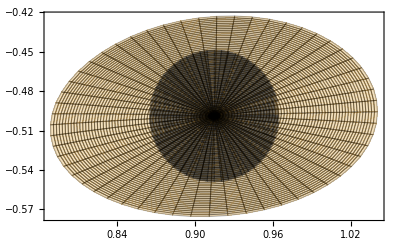

```mathematica
FP={x,y}/.FPSub;
ParametricPlot[ {
FP+r {Cos[θ],Sin[θ]},
f[FP+r {Cos[θ],Sin[θ]}]},
{θ,0, 2π},{r, 0, 0.05},
Mesh->All]
```

```mathematica
JMat=D[f[{x,y}],{{x,y}}]/.FPSub
Eigenvalues[JMat]
SingularValueList[JMat]
```

{{0.780189,2.40308},{-1.40402,0.595979}}

{0.688084+1.83453 ⅈ,0.688084-1.83453 ⅈ}

{2.53204,1.51615}

I do not think this is going to be a stable fixed point!

## Ex 2

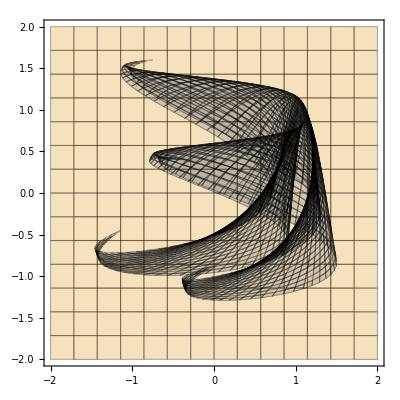

```mathematica
f[{x_,y_}]:= {0.1+0.2x +0.1y+ Cos[x *y], 0.1y-0.2x + Cos[x+y]}
ParametricPlot[{ f[{x,y}],{x,y}},{x,-2,2},{y,-2,2},
Mesh->All]
```

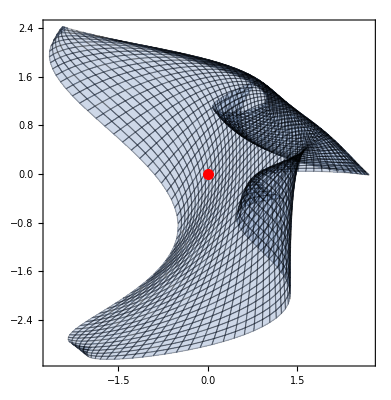

```mathematica
ParametricPlot[f[{x,y}]-{x,y},{x,-2,2},{y,-2,2},
Mesh->All,
Epilog->{Red, PointSize[0.02], Point[{0,0}]}]
```

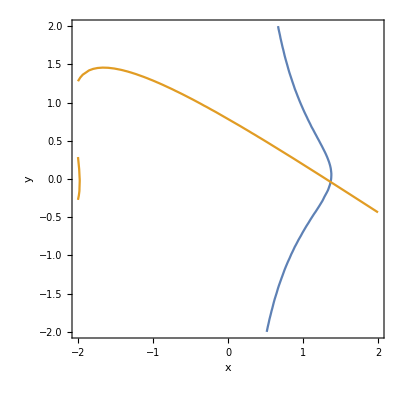

```mathematica
ContourPlot[{f[{x,y}]⟦1⟧==x,f[{x,y}]⟦2⟧==y},{x,-2,2},{y,-2,2},
Mesh->All,
FrameLabel->{"x","y"}]
```

Once we have a decent initial guess we can compute the fixed point!

```mathematica
FPSub=FindRoot[f[{x,y}]=={x,y},{x,1},{y,-0.1}]
```

{x→1.3684,y→-0.0387445}

The bad news is we do not know if there are other solutions further out in x and/or y!   We would like to know if this is stable.  First a picture.

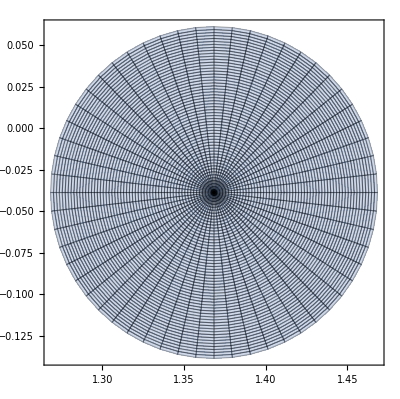

```mathematica
FP={x,y}/.FPSub;
ParametricPlot[ FP+r {Cos[θ],Sin[θ]},
{θ,0, 2π},{r, 0, 0.1},
Mesh->All]
```

{{-0.625817,-0.0473025},{1.4828,0.019964}}

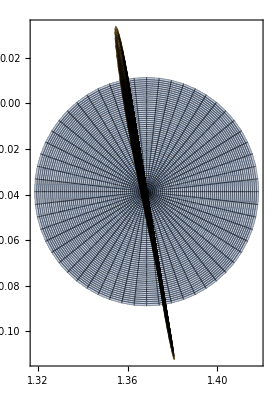

```mathematica
FP={x,y}/.FPSub;
JMat=D[f[{x,y}],{{x,y}}]/.FPSub;
{Eigenvalues[JMat],SingularValueList[JMat]}
ParametricPlot[ {
FP+r {Cos[θ],Sin[θ]},
f[FP+r {Cos[θ],Sin[θ]}]},
{θ,0, 2π},{r, 0, 0.05},
Mesh->All]
```

Still Not stable!

## Ex 3

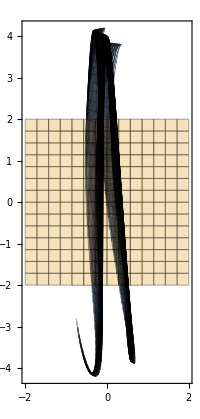

```mathematica
f[{x_,y_}]:= {0.2x +0.1y+ 0.2 Sin[x *y], 0.1y+ 4 Cos[x+y]}
ParametricPlot[{ f[{x,y}],{x,y}},{x,-2,2},{y,-2,2},
Mesh->All]
```

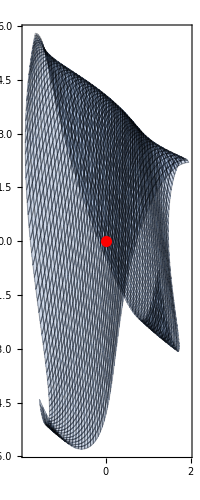

```mathematica
ParametricPlot[f[{x,y}]-{x,y},{x,-2,2},{y,-2,2},
Mesh->All,
Epilog->{Red, PointSize[0.02], Point[{0,0}]}]
```

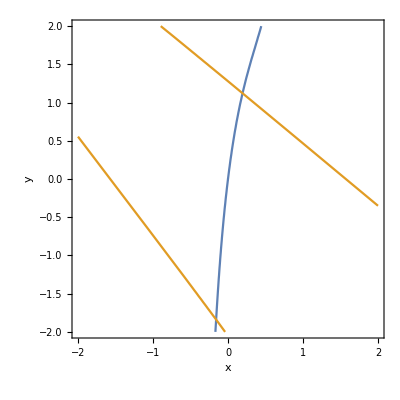

```mathematica
ContourPlot[{f[{x,y}]⟦1⟧==x,f[{x,y}]⟦2⟧==y},{x,-2,2},{y,-2,2},
Mesh->All,
FrameLabel->{"x","y"}]
```

Once we have a decent initial guess we can compute the fixed points!

```mathematica
FPSub1=FindRoot[f[{x,y}]=={x,y},{x,0},{y,1}]
FPSub2=FindRoot[f[{x,y}]=={x,y},{x,0},{y,-2}]
```

{x→0.194208,y→1.12149}

{x→-0.158191,y→-1.83927}

The bad news is we do not know if there are other solutions further out in x and/or y!   We would like to know which if any is stable.  First a picture.

{{-3.63901,0.287447},{5.41809,0.193061}}

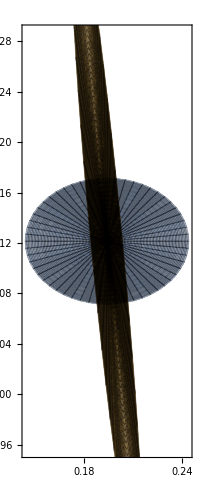

```mathematica
FP={x,y}/.FPSub1;
JMat=D[f[{x,y}],{{x,y}}]/.FPSub1;
{Eigenvalues[JMat],SingularValueList[JMat]}
ParametricPlot[ {
FP+r {Cos[θ],Sin[θ]},
f[FP+r {Cos[θ],Sin[θ]}]},
{θ,0, 2π},{r, 0, 0.05},
Mesh->All]
```

{{3.80553,-0.216511},{5.22122,0.157806}}

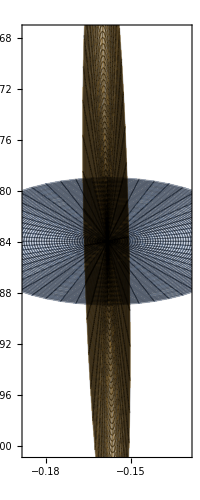

```mathematica
FP={x,y}/.FPSub2;
JMat=D[f[{x,y}],{{x,y}}]/.FPSub2;
{Eigenvalues[JMat],SingularValueList[JMat]}
ParametricPlot[ {
FP+r {Cos[θ],Sin[θ]},
f[FP+r {Cos[θ],Sin[θ]}]},
{θ,0, 2π},{r, 0, 0.05},
Mesh->All]
```

Still Not stable!

## Ex 4

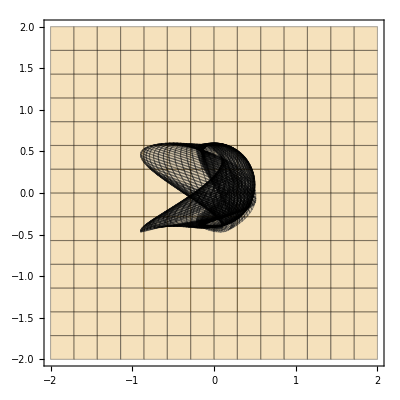

```mathematica
f[{x_,y_}]:= { 0.4 Sin[x *y]+0.5 Cos[x+2y], 0.1 Cos[x*y]-0.5Sin[x+y]}
ParametricPlot[{ f[{x,y}],{x,y}},{x,-2,2},{y,-2,2},
Mesh->All]
```

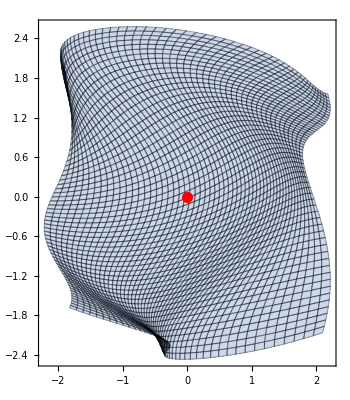

```mathematica
ParametricPlot[f[{x,y}]-{x,y},{x,-2,2},{y,-2,2},
Mesh->All,
Epilog->{Red, PointSize[0.02], Point[{0,0}]}]
```

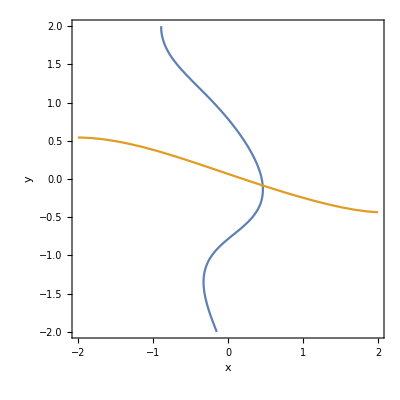

```mathematica
ContourPlot[{f[{x,y}]⟦1⟧==x,f[{x,y}]⟦2⟧==y},{x,-2,2},{y,-2,2},
Mesh->All,
FrameLabel->{"x","y"}]
```

Once we have a decent initial guess we can compute the fixed points!

```mathematica
FPSub=FindRoot[f[{x,y}]=={x,y},{x,0},{y,0}]
```

{x→0.462935,y→-0.0847117}

The bad news is we do not know if there are other solutions further out in x and/or y!   We would like to know which if any is stable.  First a picture.

{{-0.582792,-0.0585704},{0.686085,0.0497523}}

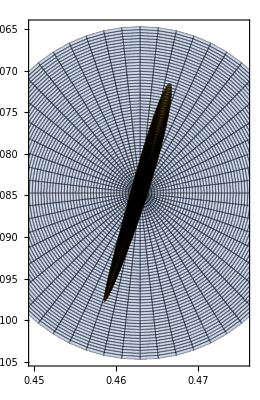

```mathematica
FP={x,y}/.FPSub;
JMat=D[f[{x,y}],{{x,y}}]/.FPSub;
{Eigenvalues[JMat],SingularValueList[JMat]}
ParametricPlot[ {
FP+r {Cos[θ],Sin[θ]},
f[FP+r {Cos[θ],Sin[θ]}]},
{θ,0, 2π},{r, 0, 0.02},
Mesh->All]
```

Stable!

```mathematica
ϵ=0.02; MaxIter=32;
p0=FP+ϵ RandomReal[{-1,1},2];
NestList[ f,p0,MaxIter]
```

{{0.459062,-0.0806933},{0.463197,-0.084771},{0.462894,-0.084806},{0.462952,-0.0846491},{0.462925,-0.0847486},{0.46294,-0.0846901},{0.462931,-0.0847242},{0.462936,-0.0847044},{0.462933,-0.0847159},{0.462935,-0.0847092},{0.462934,-0.0847131},{0.462935,-0.0847108},{0.462934,-0.0847122},{0.462935,-0.0847114},{0.462935,-0.0847118},{0.462935,-0.0847116},{0.462935,-0.0847117},{0.462935,-0.0847116},{0.462935,-0.0847117},{0.462935,-0.0847117},{0.462935,-0.0847117},{0.462935,-0.0847117},{0.462935,-0.0847117},{0.462935,-0.0847117},{0.462935,-0.0847117},{0.462935,-0.0847117},{0.462935,-0.0847117},{0.462935,-0.0847117},{0.462935,-0.0847117},{0.462935,-0.0847117},{0.462935,-0.0847117},{0.462935,-0.0847117},{0.462935,-0.0847117}}